```mathematica
PointGenerator[num_, polygon_]:=Block[{
P = List[],Pvector=List[],
PI,PIvector,
i,t,
minX= Infinity,minY=Infinity,
maxX = -1, maxY =-1,
length,
result 
},
length = Length[polygon];

For[i = 1, i ≤ length,++i,
If[Part[Part[polygon,i],1]<minX,minX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]<minY,minY =Part[Part[polygon,i],2]];

If[Part[Part[polygon,i],1]>maxX,maxX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]> maxY,maxY =Part[Part[polygon,i],2]];
];
For[ t = 0, t< num, t++;,
	PI={RandomInteger[{minX, maxX}], RandomInteger[{minY, maxY}]}; 
	 PIvector = {RandomInteger[{-50, 50}], RandomInteger[{-50, 50}]}; 
	AppendTo[Pvector,PIvector];
	AppendTo[P,PI];
];
result ={P,Pvector};
Return[result];];
```

```mathematica
PoligonPreCount[SPolygon_] :=Block[{
P = List[], 
S =List[], 
result,n,
smallPolygonLength
},
smallPolygonLength = Length[SPolygon];
For[n = 1, n <smallPolygonLength , ++n,
AppendTo[P,Part[SPolygon, n+1]-Part[SPolygon, n]];
];
Return [P]];
```

```mathematica
PolygonSizes [polygon_]:= Block[{
minX= Infinity,minY=Infinity,
maxX = -1, maxY =-1,
length,
result
},
length = Length[polygon];

For[i = 1, i ≤ length,++i,
If[Part[Part[polygon,i],1]<minX,minX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]<minY,minY =Part[Part[polygon,i],2]];

If[Part[Part[polygon,i],1]>maxX,maxX =Part[Part[polygon,i],1]];
If[Part[Part[polygon,i],2]> maxY,maxY =Part[Part[polygon,i],2]];
];
result = {{minX,minY},{maxX, maxY}};
Return[result]
]
```

```mathematica
move[polygon_,SPPC_, PSize_] := Block[{
P=List[],
PI,P1,
VI,V1,
b,a,
i,n,n2,
length,
polygonLength,
flag =1,
result
},
length = Length[points];
polygonLength = Length[polygon];
For[i = 1, i <= length,i++,
If[Part[vectors, i] == {0,0},Print[Part[points,i], i],

PI=Part[points,i]+(Part[vectors,i]);
P1 = Part[points,i];


If[Test[PI,PSize],
Part[points,i] = PI;,
For[n = 1, n <polygonLength &&  flag == 1, ++n,
If[((Det[{Part[SPPC, n],PI-Part[polygon,n]}]*Det[{Part[SPPC, n],P1-Part[polygon,n]}] > 0)||
		 (Det[{PI-P1,Part[polygon,n]-P1}]*Det[{PI-P1,Part[polygon,n+1]-P1}]>0 ))
			,
, 
b=Part[polygon, n+1]-Part[polygon, n];
a =Part[vectors,i];
VI = 2((a.b)/(b.b))*b - a;
Part[vectors,i] = VI;
flag =0];
];
If[flag == 1, 
Print["хм..."]];


];
];
];
result = NearestPair[points];
minLine = result[[1]];
If[result[[2]] < 200,textField = "Бадабум!!!", textField = " "];

Return[points]];
```

```mathematica
SegmentLength[P1_,P2_]:= Block[{
Px2,Py2
},
Px2 = (Part[P1,1]-Part[P2,1])*(Part[P1,1]-Part[P2,1]);
Py2 = (Part[P1,2]-Part[P2,2])*(Part[P1,2]-Part[P2,2]);

Return[Sqrt[Px2 + Py2]]
]
```

```mathematica
Test[point_, PSize_] := Block[{
flag = True,
X,Y,
minX,minY,
maxX, maxY,
},
X= Part[point,1];
Y = Part[point, 2];

minX = Part[Part[PSize, 1],1]; minY = Part[Part[PSize, 1],2];
maxX = Part[Part[PSize, 2],1]; maxY = Part[Part[PSize, 2],2];
If[(maxX > X > minX)&&(maxY> Y > minY),,flag = False];
Return[flag]]
```

{{{4773,3298},{5106,3480}},√144013}

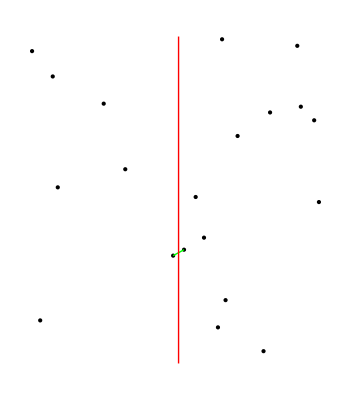

{896,9879/2,2978,12649/2,17255/2,7640,11863/2}

```mathematica
NearestPair[points_] :=Block[{
Points = List[],
result
},
Points = points;
Points = SortBy[Points, First];

result =NearestPairHelper[Points];

Return[result]]

NearestPairHelper[Points_] :=Block[{
P1 = List[],P2= List[],
minLength = Infinity,nextLength,
result,
length,
firstResult,secondResult,
halfLength, prePoints = List[],
mid,i,n,flag
},
length = Length[Points];
If[length>3,
halfLength = IntegerPart[length/2];



firstResult = NearestPairHelper[Points[[1;;halfLength]]];
secondResult =NearestPairHelper[Points[[halfLength+1;;length]]];
If[Part[firstResult, 2]< Part[secondResult, 2],result = firstResult, result = secondResult];
minLength = result[[2]];

mid = (Part[Part[Points,halfLength],1]+ Part[Part[Points,halfLength+1],1])/2;
AppendTo[mids,mid];

For[i  = 1 , i ≤ length, i++,
If[Abs[Part[Part[Points,i],1] - mid ]< minLength, AppendTo[prePoints,Part[Points,i]];];
];
prePoints = SortBy[prePoints, Last];
length = Length[prePoints];
For[i = 1, i < length, ++i,

flag = True;
For[n = i+1, n ≤ length&& n ≤ i+7&&flag, ++n,
If[Part[Part[prePoints,n],2]-Part[Part[prePoints,i],2]< minLength,
nextLength = SegmentLength[Part[prePoints,i],Part[prePoints,n]];
If[minLength  > nextLength,minLength = nextLength; P1 = Part[prePoints,i]; P2 = Part[prePoints,n]];
,
flag = False;
];
];
];
If[result[[2]] > minLength,result = {{P1, P2}, minLength};];

,
For[i = 1, i < length, ++i,
For[n = i+1, n ≤ length, n++,
nextLength = SegmentLength[Part[Points,i],Part[Points,n]];
If[minLength  > nextLength,minLength = nextLength; P1 = Part[Points,i]; P2 = Part[Points,n]];
];
];
result = {{P1, P2}, minLength};
];

Return[result];]


mids= List[];
myPoints = {{1242,5387},{455,9554},{7540,376},{5718,3848},{9236,4937},{8573,9716},{4773,3298},{5106,3480},{5463,5092},{2648,7947},{6378,1937},{704,1317},{8682,7854},{9090,7438},{3308,5941},{6271,9916},{6746,6958},{6145,1104},{1088,8779},{7740,7678}};
ncdc= NearestPair[myPoints]
Graphics[{Point[myPoints], Green,Line[Part[ncdc,1]], Red, Line[{{mids[[2]], 0},{mids[[2]], 10000}}]}]
mids
```

```mathematica
square = {{-1,-1},{-1,10001},{10001,10001},{10001,-1},{-1,-1}};
pointVector = PointGenerator[20, square];
points = Part[pointVector,1]
vectors = Part[pointVector, 2];
BPPC = PoligonPreCount[square];
PSize = PolygonSizes[square];
minLine;
textField;

Graphics[{Line[{square}], Red,Point[{square}],Blue, Point[{Dynamic[move[square,BPPC,PSize]]}], Green, Line[Dynamic[minLine]], Red, Text[Dynamic[textField] ,Center]}]
```

{{6548,6182},{4932,4485},{7740,9648},{5264,1065},{2335,6852},{4723,4499},{5914,2986},{6765,5959},{3646,5122},{7528,8153},{6505,9846},{1324,1904},{9263,1666},{1533,100},{4955,3690},{6433,1269},{4572,271},{8070,5828},{5354,1759},{3181,2826}}

-Graphics-